### Setting up board

```mathematica
getTileType[board_,sector_,row_,column_]:=board⟦sector,row,column,1⟧
```

#### Mine setup

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
boardSetUp[numOfRows_,factor_]:= 
Module[
{tiles = 8*numOfRows^2 ,
lst = Table[{},{x,1,8}],
row,section,
numOfTiles},
remainingMineCount = factor * tiles;
(*For loop for stacking *)
For[row = 1,row≤ numOfRows,row++,
(*Goes through each section*)
For[section = 1, section≤ 8, section++,
AppendTo[lst⟦section⟧,{}];
(*Loop to add tiles to each section & row*)
For[numOfTiles= 1, numOfTiles≤ 2*row - 1,numOfTiles++,
tile = RandomChoice[{remainingMineCount/tiles,(tiles - remainingMineCount)/tiles}->{Red,Blue}];
If[tile == Red,
remainingMineCount--;
];
tiles--;
AppendTo[lst⟦section⟧⟦row⟧,tile]
]
]
];
Return [lst]
]
```

```mathematica
Grid[boardSetUp[3,0.25]]
```

{RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0]}
{RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}
{RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}
{RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}
{RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}
{RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}
{RGBColor[1, 0, 0]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}
{RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}

#### Triangle point setup

Setting up coordinates of triangles.

```mathematica
(*Construct a single row of triangles for the tiling*)
constructTiledTriangleRow[numItems_,offset_]:=Module[
{zigzag=Riffle[
Table[{pointX,Sin[(3π)/8]}+offset,{pointX,-(numItems+1)/2 Cos[(3π)/8],(numItems+1)/2 Cos[(3π)/8],2Cos[(3π)/8]}],
Table[{pointX,0}+offset,{pointX,-(numItems-1)/2 Cos[(3π)/8],(numItems-1)/2 Cos[(3π)/8],2Cos[(3π)/8]}]

]
},
Return[Table[{zigzag⟦i⟧,zigzag⟦i+1⟧,zigzag⟦i+2⟧},{i,numItems}]]
]
```

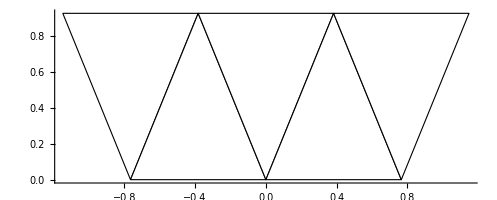

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[constructTiledTriangleRow[5,{0,0}]]},Axes->True]
```

```mathematica
(*Constructs a "big" triangle*)
constructTiledTriangle[numRows_]:=Table[constructTiledTriangleRow[numTriangles,{0,(numTriangles-1)/2*Sin[(3π)/8]}],{numTriangles,1,2numRows-1,2}]
```

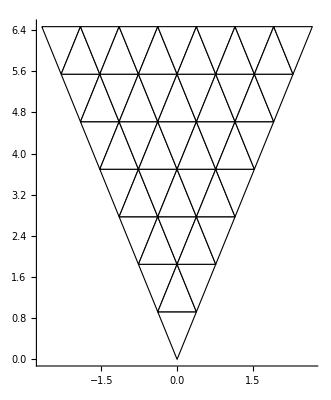

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@constructTiledTriangle[7]]},Axes->True]
```

```mathematica
(*Rotate points of a triangle created from constructTiledTriangle*)
rotateMassTriangle[triangles_,θ_]:=Table[Table[Table[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.point,{point,triangle}],{triangle,row}],{row,triangles}]
```

```mathematica
(*Construct triangle points for the board tiles*)
createBoardSkeleton[numRows_]:=Table[rotateMassTriangle[constructTiledTriangle[numRows],θ],{θ,2π,π/4,-π/4}]
```

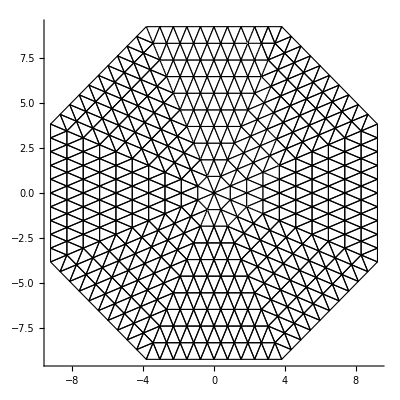

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@Join@@createBoardSkeleton[10]]},Axes->True]
```

### Other

```mathematica
ModelToView[board_]:= 

Module[
{graphics = {},x,y},
	For[x=1,x≤ 30,x++,
						AppendTo[graphics,{}];
						For[y = 1,y≤ 16,y++,
							If[board⟦x⟧⟦y⟧⟦1⟧=== Red,
							AppendTo[graphics,{Red,Circle[{y+0.5,x-0.5},0.5]}],
							AppendTo[graphics,{Blue,Circle[{y+0.5,x-0.5},0.5],Black,Text[board⟦x⟧⟦y⟧⟦1⟧,{y+0.5,x-0.5}]}]
							]
						
						]
					];
				Return[graphics];
					
					
					


				]
```

```mathematica
minesweeperBoard[]:= Module[
{minecount,row,section,x,y},
(*Mine, status, probability*)
(*Red are mines*)

For[x = 2,x ≤ 29,x++,
For[y = 2,y≤ 15,y++,
If[board⟦x⟧⟦y⟧⟦1⟧ == Blue,
	board⟦x⟧⟦y⟧⟦1⟧ = borderingMines[board,x,y];
	(*riskMap[x,y];*)
	]
	]
];
Return[Null];

]
```

```mathematica
borderingMines[x_,y_]:= Module[{count = 0,X,Y},
						For[X = x-1,X ≤ x+1,X++,
							For[Y = y-1,Y≤ y+ 1,Y++,
								If[board⟦X⟧⟦Y⟧⟦1⟧ == Red,
								count++;
								]
							]
						];
						Return[count];
						]
```

```mathematica
riskMap[x_,y_]:= Module[{count,X,Y},
					count = borderingMines[x,y];
				For[X = x-1,X ≤ x+1,X++,
							For[Y = y-1,Y≤ y+ 1,Y++,
								
								board⟦X⟧⟦Y⟧⟦3⟧  += count/9;
								
							]
						];

]
```

```mathematica
click[x_,y_]:= Module[{},
				If[board⟦x⟧⟦y⟧⟦1⟧=== Red,

				Print["game over"],
				board⟦x⟧⟦y⟧⟦2⟧ = 1
				
					];
				


				]
```

```mathematica
minesweeperBoard[]
board
```

$Aborted[]